```mathematica
ppd[d1_:0.1,d2_:0.05,b_:0.1,p1_:0.25,p2_:0.05,N_:3000,f10_,f20_]:=
Block[{r,K,p,f1,f2,t,eqs,init},
r=2b-d2;
K=(2b-d2)/(2b);
p=p1+p2+b;
eqs = {
D[f1[t], t]==-d1*f1[t]+2p1*f1[t]*f2[t],
D[f2[t], t]==r*f2[t]*(1-f2[t]/K)-2p*f1[t]*f2[t]
};
init={
f1[0]==f10,
f2[0]==f20
};
{eqs,init}//Flatten
]
tmax=500;
sol1=NDSolve[ppd[1/30,2/30]//Evaluate,{f1,f2},{t,0,tmax}];
sol2=NDSolve[ppd[0.2,0.8]//Evaluate,{f1,f2},{t,0,tmax}];
sol3=NDSolve[ppd[0.8,0.2]//Evaluate,{f1,f2},{t,0,tmax}];
```

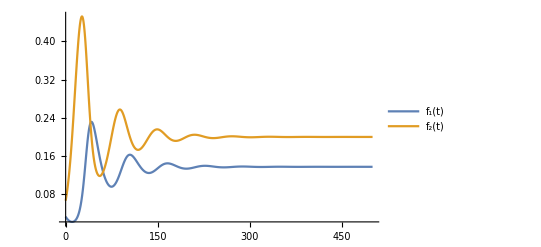

```mathematica
Plot[{f1[t]/.sol1[[1]],f2[t]/.sol1[[1]]},{t,0,tmax},PlotLegends->{"f_1(t)","f_2(t)"},PlotRange->Full]
```

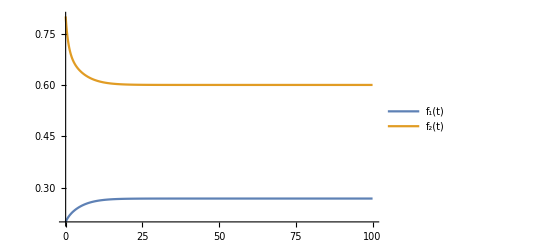

```mathematica
Plot[{f1[t]/.sol2[[1]],f2[t]/.sol2[[1]]},{t,0,tmax},PlotLegends->{"f_1(t)","f_2(t)"},PlotRange->Full]
```

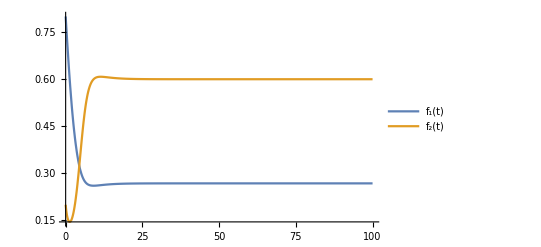

```mathematica
Plot[{f1[t]/.sol3[[1]],f2[t]/.sol3[[1]]},{t,0,tmax},PlotLegends->{"f_1(t)","f_2(t)"},PlotRange->Full]
```

```mathematica
ppd1[d1_:0.1,d2_:0.05,b_:0.1,p1_:0.25,p2_:0.05,N_:3000]:=
Block[{r,K,p,f1,f2,t,eqs},
r=2b-d2;
K=(2b-d2)/(2b);
p=p1+p2+b;
eqs = {
-d1*f1+2p1*f1*f2,
r*f2*(1-f2/K)-2p*f1*f2
};
eqs
]
```

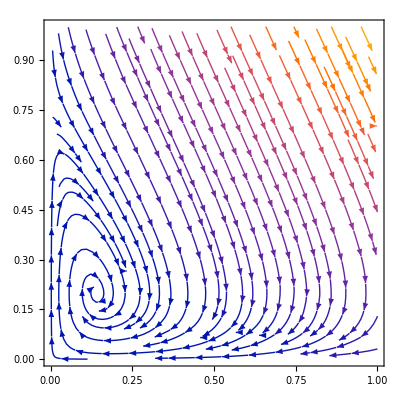

```mathematica
StreamPlot[ppd1[],{f1,0,1},{f2,0,1}]
```

```mathematica
Block[
{d1=0.3,
d2=0.05,
b=0.8,
p1=0.25,
p2=0.05,
r=2b-d2,
K=r/2b,
p=p1+p2+b},
J = {{0, (p1*r-d1*b)/p},{-p*d1/p1,-b*d1/p1}};
f=√((p*d1/p1)*(p1*r-d1*b)/p)/(2π);
T=1/f;
J//MatrixForm;
Eigenvalues[J]
]
```

{-0.711084,-0.248916}

```mathematica
Eigenvalues[J]
```

{-0.02+0.102956 ⅈ,-0.02-0.102956 ⅈ}